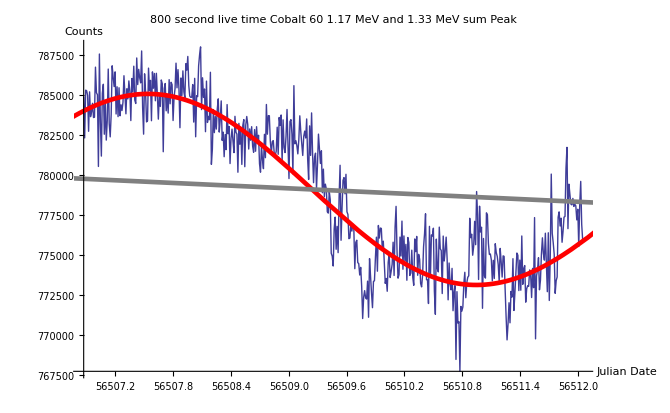

```mathematica
Subscript[N, 0] = 780000;
HalfLife = 1925.28;
T = 1.72154×10^9;
Subscript[N, f] = Subscript[N, 0] ⅇ^(-(Log[2](t -56506))/HalfLife) + 5500Sin[(6t)/(2π)+2/8π];
Subscript[N, k] = Subscript[N, 0] ⅇ^(-(Log[2](t -56506))/HalfLife) ;
data = Import["/Users/spenceraxani/Documents/499_Thesis/data/datapack/L2-008_germanium_data_1.17MeV.txt","Table"];
A = ListLinePlot[data,Joined->True,PlotLabel->Style[Framed["800 second live time Cobalt 60 
1.17 MeV and 1.33 MeV sum Peak"]],AxesLabel->{"Julian Date","Counts"}];
decay = Plot[Subscript[N, f],{t,56470,56600},PlotStyle->{{Thickness[0.005],Red}}];
decay2 = Plot[Subscript[N, k],{t,56470,56600},PlotStyle->{{Thickness[0.005],Gray}}];
deadtime = Import["/Users/spenceraxani/Documents/499_Thesis/data/datapack/L2-008_germanium_dead_time.txt","Table"];
Show[A,decay, decay2]
B=ListPlot[deadtime,Joined->True];
```